# Brownian Motion

This Mathematica Notebook accompanies the calculations pertaining to the analysis of heavy and light quark test strings undergoing Brownian motion in section (4) and section (5) of the dissertation, 'Understanding Heavy and Light Quark Brownian Motion from AdS/CFT : Analytical Analysis of Open String Evolution in the Bulk', by A. Mes

```mathematica
(*PacletInstall["https://rulebasedintegration.org/Rubi-4.16.1.0.paclet"]*)
<<Rubi` (*Package for integration*)
```

```mathematica
$Assumptions=rstar∈Reals&&r∈Reals &&rH∈Reals &&L∈Reals;
SetAttributes[rH,Constant];SetAttributes[L,Constant];
```

## Analysing Heavy Quark Brownian Motion (Section 4)

Section (4) focuses on calculating an external heavy quark’s diffusion coefficient in the bulk AdS_3-Schwarzschild spacetime. The dual description of the on-mass-shell heavy quark exhibiting Brownian motion in the thermal plasma – an open string attached at the anti-de Sitter boundary and hanging towards the horizon undergoing transverse fluctuations – is used to compute the mean-squared transverse displacement of the string’s boundary endpoint s^2(t; 3). The diffusion coefficient is extracted at late times.

### Leading Order String Behaviour: Test Strings in AdS_3-Schwarzschild (Subsection 4.2.2)

Consider a test string in AdS_3-Schwarzschild set up as in figure (2), page 15. Examining the leading order behaviour of the string (no transverse fluctuations are present), the equations of motion with respect to the boundary and initial conditions can be solved in order to find the embedding functions (X^μ)_(AdS3-Sch)(t,σ).

The AdS_d - Schwarzschild metric is given by

```mathematica
(*Equations 4.33 and 4.34*)
```

```mathematica
ds2[r_,h_,t_, X_]:= r^2/L^2*(-h*Dt[t]^2+Dt[X]^2)+L^2/r^2 Dt[r]^2/h;
hAdSd[r_,d_]:=1-rH^(d-1)/r^(d-1);
```

The Hawking temperature of the black-brane in AdS_d-Schwarzschild – corresponding to the temperature of the thermal plasma in the boundary theory – is

```mathematica
(*Equations 4.35*)
```

```mathematica
T[d_]:=((d-1) rH)/(4 π L^2)
```

Defining the tortoise co-ordinate, r_*, to be

```mathematica
(*Equation 4.37*)
```

```mathematica
rstar[r_,d_]:=L^2*Int[1/r^2 1/hAdSd[r,d],r]
```

```mathematica
(*Equation 4.38*)
```

```mathematica
rstar[r,d]
```

-(L^2 Hypergeometric2F1[1,1/(-1+d),-d/(1-d),r^(1-d) rH^(-1+d)])/r

In AdS_3-Schwarzschild, the tortoise co-ordinate becomes

```mathematica
(*Equation 4.39*)
```

```mathematica
rstarADS3=rstar[r,d]/.d->3
```

-(L^2 ArcTanh[rH/r])/rH

The inverse tortoise coordinate is therefore given by

```mathematica
(*Equation 4.40*)
```

```mathematica
rAdS3sol=Refine[Solve[rstar==rstarADS3,r],{L>0,rH≥ 0}];
rAdS3=r/.rAdS3sol;
rAdS3[[1]]
```

-rH Coth[(rH rstar)/L^2]

The AdS_3 - Schwarzschild metric is given by

```mathematica
(*Equations 4.41*)
```

```mathematica
ds2AdS3=ds2[r,h,t, X]/.h->hAdSd[r,3]//Simplify
```

((L^4 Dt[r]^2)/(r^2-rH^2)+(-r^2+rH^2) Dt[t]^2+r^2 Dt[X]^2)/L^2

The AdS_3 - Schwarzschild metric can now be converted into (t, r_*) coordinates using Eq.(4.40)

```mathematica
(*Equations 4.43*)
```

```mathematica
ds2AdS3/.r->rAdS3[[1]]//Simplify//Expand
```

(rH^2 Csch[(rH rstar)/L^2]^2 Dt[rstar]^2)/L^2-(rH^2 Csch[(rH rstar)/L^2]^2 Dt[t]^2)/L^2+(rH^2 Coth[(rH rstar)/L^2]^2 Dt[X]^2)/L^2

The remainder of the subsection (pages 22-23) focusses on  find the embedding functions (X^μ)_(AdS3-Sch)(t,σ) (Eq.(4.50)). In the process, the identification Eq.(4.52) is made.

```mathematica
(*Equations 4.52*)
```

```mathematica
rid[σ_]=-rH Coth[(rH (rstar+σ))/L^2];
```

### Fluctuating Test String Dynamics: Calculating the Heavy Quark’s Mean-Squared Displacement s^2(t) in AdS_3-Schwarzschild (Subsection 4.3.2)

In AdS_3-Schwarzschild, the equations of motion for the transverse fluctuations, Eq.(4.66), become

```mathematica
(*Equation 4.74*)
```

```mathematica
EoMtr[t_,r_,X_]:=-D[X,{t,2}] + (r^2-rH^2)/(L^4 r^2)*D[(r^2(r^2-rH^2) D[X,r]),r] ==0;
```

In parameter world-sheet coordinates (t, σ)

```mathematica
r^2(r^2-rH^2)/.r-> rid[σ]//Simplify
```

rH^4 Coth[(rH (rstar+σ))/L^2]^2 Csch[(rH (rstar+σ))/L^2]^2

```mathematica
(r^2-rH^2)/(L^4 r^2)/.r-> rid[σ]//Simplify
```

(Sech[(rH (rstar+σ))/L^2]^2)/L^4

```mathematica
(*Equation 4.75*)
```

```mathematica
EoMtσ[t_,σ_,X_]:=-D[X,{t,2}] + 1/(Coth[(rH (rstar+σ))/L^2]^2)*D[(Coth[(rH (rstar+σ))/L^2]^2 D[X,σ]),σ]==0;
```

To proceed in solving the linear and homogeneous partial differential equation Eq.(4.74) – or Eq.(4.75) in (t,σ) coordinates – the method laid out in de Boer et al. [1] is followed. Explicitly, consider a mode expansion in X,

```mathematica
(*Equation 4.76*)
```

```mathematica
Xsep[t_,r_]:=fω[r]*ⅇ^(-ⅈ ω t)
```

where, it is found that fω(r) satisfies the ODE :

```mathematica
(*Equation 4.77*)
```

```mathematica
EoMsep[r_,fω_]:=ω^2 fω + (r^2-rH^2)/(L^4 r^2)*D[(r^2(r^2-rH^2) D[fω,r]),r]==0
```

Defining the dimensionless quantity, ν=(L^2 ω)/rH

```mathematica
(*Equations 4.78*)
```

```mathematica
ω1:= (ν rH)/L^2;
```

This ODE has two linearly independent solutions

```mathematica
(*Equations 4.80*)
```

```mathematica
fωplus:= 1/(1+ⅈ ν)(r+ ⅈ rH ν)/r ((r-rH)/(r+rH))^((ⅈ ν)/2)
fωminus:= 1/(1-ⅈ ν)(r- ⅈ rH ν)/r ((r-rH)/(r+rH))^(-(ⅈ ν)/2)
```

```mathematica
(*Consistency Check:*)
(*EoMsep[r,fωplus][[1]]//Simplify
EoMsep[r,fωminus][[1]]//Simplify*)
```

From Eq.(4.84) it is apparent that (f^±)_ω(r) denotes out-going (+) and in-falling (−) basis modes. The general solution to the ODE, f_ω(r), is a linear combination of these modes

```mathematica
(*Equations 4.85*)
```

```mathematica
fω = fωplus+Bω*fωminus;
```

This ODE has two linearly independent solutions

```mathematica
(*Equations 4.87*)
```

```mathematica
B=Simplify[Expand[Solve[D[fω,r]==0,Bω]/. ω->ω1]]
```

{{Bω→(((r-rH)/(r+rH))^(ⅈ ν) (ⅈ+ν) (-ⅈ rH+r ν))/((-ⅈ+ν) (ⅈ rH+r ν))}}

```mathematica
Bomega=Bω/.B;
Bω=Bomega[[1]]
```

(((r-rH)/(r+rH))^(ⅈ ν) (ⅈ+ν) (-ⅈ rH+r ν))/((-ⅈ+ν) (ⅈ rH+r ν))

To leading order the induced world-sheet metric is given by Eq.(4.60). For d= 3, this metric simplifies to

```mathematica
(*Equation 4.70*)
```

```mathematica
gtt[r_]:= - (r^2-rH^2)/L^2;
```

```mathematica
gσσ[r_]:= D[r, σ]^2*(L^2/(r^2-rH^2));
```

Converting this metric into (t, r_*) coordinates

```mathematica
(*Equation 4.95*)
```

```mathematica
gttTort= gtt[rid[σ]]//Simplify
```

-(rH^2 Csch[(rH (rstar+σ))/L^2]^2)/L^2

```mathematica
gσσTort= gσσ[rid[σ]]//Simplify
```

(rH^2 Csch[(rH (rstar+σ))/L^2]^2)/L^2

The determinant of the leading order induced world-sheet metric in (t, r_*) coordinates is

```mathematica
(*Equation 4.96*)
```

```mathematica
detg =gttTort*gσσTort
```

-(rH^4 Csch[(rH (rstar+σ))/L^2]^4)/L^4

To leading order the inverse induced world-sheet metric is given by

```mathematica
(*Equation 4.71*)
```

```mathematica
inversegtt[r_]:= - (L^2/(r^2-rH^2));
```

```mathematica
inversegσσ[r_]:= 1/D[r, σ]^2*((r^2-rH^2)/L^2);
```

Converting this metric into (t, r_*) coordinates

```mathematica
(*Equation 4.95*)
```

```mathematica
inversegttTort= inversegtt[rid[σ]]//Simplify
```

-(L^2 Sinh[(rH (rstar+σ))/L^2]^2)/rH^2

```mathematica
inversegσσTort= inversegσσ[rid[σ]]//Simplify
```

(L^2 Sinh[(rH (rstar+σ))/L^2]^2)/rH^2

To quantize the theory, the scalar field X(t,σ)and its canonically conjugate momentum P^t(t,σ) are promoted to operators and suitable commutation relations are imposed. The position operator is given by Eq.(4.92); and the conjugate momentum operator is given by Eq.(4.93)

```mathematica
(*Equation 4.95 - line 3*)
```

```mathematica
(r^2/L^2)/.r-> rid[σ]//Simplify
```

(rH^2 Coth[(rH (rstar+σ))/L^2]^2)/L^2

```mathematica
inversegttTort
```

-(L^2 Sinh[(rH (rstar+σ))/L^2]^2)/rH^2

```mathematica
Refine[Sqrt[(-detg)],{rH≥0,L≥0,Csch[(rH (rstar+σ))/L^2]≥0}]
```

(rH^2 Csch[(rH (rstar+σ))/L^2]^2)/L^2

```mathematica
(*Equation 4.95 - line 4*)
```

```mathematica
Refine[Sqrt[(-detg)],{rH≥0,L≥0,Csch[(rH (rstar+σ))/L^2]≥0}]*inversegttTort*(r^2/L^2)/.r-> rid[σ]//Simplify
```

-(rH^2 Coth[(rH (rstar+σ))/L^2]^2)/L^2

In order to fix the normalization constant A_ω canonical commutation relations between X(t, σ) and P^t(t, σ) are enforced, Eq.(4.98).

```mathematica
(*Equation A.55*)
```

```mathematica
fw1[σ_,rH_,rsstar_,r_,ω_,r0_,ν_,σf_] := 1/(1+ ⅈ ν)(r + ⅈ rH ν)/r Exp[ ⅈ ω (rsstar + σ)]+((1- ⅈ ν)/(1+ ⅈ ν) (1 + ⅈ r0 ν)/(1 - ⅈ r0 ν)Exp[ ⅈ 2 ω (rsstar +σf)])1/(1- ⅈ ν)(r - ⅈ rH ν)/r Exp[ -ⅈ ω (rsstar + σ)];

fwconj1[σ_,rH_,rsstar_,r_,ω_,r0_,ν_,σf_]=Simplify[ComplexExpand[Conjugate[fw1[σ,rH,rsstar,r,ω,r0,ν,σf]]]];
```

```mathematica
(*Near horizon limit:r_(s*)-> - ∞, r -> Subscript[r, H] (thereforeSubscript[r, 0]-> 1); andSubscript[σ, f]-> 0*)
```

```mathematica
1/2(fw1[σ1,rH,rsstar,rH,ω,1,ν,0]*fwconj1[σ2,rH,rsstar,rH,ω,1,ν,0]+ fw1[σ2,rH,rsstar,rH,ω,1,ν,0]*fwconj1[σ1,rH,rsstar,rH,ω,1,ν,0]) /. ν-> (L^2 ω)/rH//Simplify//ExpandAll
```

ⅇ^(-ⅈ σ1 ω-ⅈ σ2 ω)+ⅇ^(ⅈ σ1 ω-ⅈ σ2 ω)+ⅇ^(-ⅈ σ1 ω+ⅈ σ2 ω)+ⅇ^(ⅈ σ1 ω+ⅈ σ2 ω)

Eq.(A.55) is used to fix the normalization constant A_ω . One finds

```mathematica
(*Equation 4.100*)
```

```mathematica
Aω = L/rH √(π α)/ω;
```

With the constants B_ω and A_ω (Eqs.(4.90, 4.100) respectively) found, the general solution for transverse equations of motion (Eq.(4.91)) is completely determined.The displacement of the boundary endpoint as the test string undergoes these transverse fluctuations can now be calculated. Following the calculations on pages 31-32, the string boundary endpoint’s mean-squared transverse displacement is calculated in Eq.(4.109).

```mathematica
(*Integrand of Equation 4.109*)
```

```mathematica
s2[t_]:=β^2/(4 π^2 √λ)*1/(ⅇ^(β ω)-1)1/ω*fω1*fωconj1*(2-ⅇ^(-ⅈ ω t)-ⅇ^(ⅈ ω t))
```

### Fluctuating Test String Dynamics: The Limiting Cases of s^2(t) (Subsection 4.3.3)

In this subsection the behaviour of s^2(t), Eq.(4.109), in the asymptotic early and late time limits is considered.

Inputting Eqs.(4.83, 4.85, 4.90) to calculate f_ω(σf) f_ω^*(σf), yield

```mathematica
$Assumptions={L >0,L ϵ Reals, r >0,r1 >0, r2 >0,rH>0,r>rH,r1>rH,r2>rH, rH ϵ Reals, r ϵ Reals,r1 ϵ Reals, r2 ϵ Reals, ω ≥0,ω ϵ Reals, σf≥0,σf ϵ Reals,σ1≥0,σ1 ϵ Reals,σ2≥0,σ2 ϵ Reals, rsstar ϵ Reals};
fω
fωconj=Conjugate[fω]//ComplexExpand//Simplify//TrigToExp
```

(((r-rH)/(r+rH))^((ⅈ ν)/2) (ⅈ+ν) (-ⅈ rH+r ν) (r-ⅈ rH ν))/(r (1-ⅈ ν) (-ⅈ+ν) (ⅈ rH+r ν))+(((r-rH)/(r+rH))^((ⅈ ν)/2) (r+ⅈ rH ν))/(r (1+ⅈ ν))

(2 rH ((r-rH)^2/(r+rH)^2)^(-(ⅈ ν)/4))/(rH+ⅈ r ν)+(2 ⅈ rH ((r-rH)^2/(r+rH)^2)^(-(ⅈ ν)/4) ν)/(rH+ⅈ r ν)

```mathematica
s2tsimplified = s2[t]/.{fω1-> fω,fωconj1-> fωconj}//Simplify
```

-(ⅇ^(-ⅈ t ω) (-1+ⅇ^(ⅈ t ω))^2 rH^2 β^2 (-ⅈ+ν) (ⅈ+ν))/((-1+ⅇ^(β ω)) π^2 √λ (rH-ⅈ r ν) (rH+ⅈ r ν) ω)

```mathematica
ExpToTrig[Expand[ⅇ^(-ⅈ t ω) (-1+ⅇ^(ⅈ t ω))^2]](*Using Cos(2x)=1-2 Sin^2(x), this expression becomes -4 Sin^2(tω/2)*)
```

-2+2 Cos[t ω]

Simplifying s2t, the mean-squared transverse displacement becomes

```mathematica
(*Integrand of Equation 4.110*)
```

```mathematica
s2t[t_]= (4 β^2)/(π^2 √λ)1/ω(1+ν^2)/(1+ r0^2 ν^2)Sin[(ω t)/2]^2/(ⅇ^(β ω)-1);
```

The integral in Eq.(4.110) is tricky to analytically evaluate. Following the insights of de Boer et al.[1], the integral can be broken into two parts, integrals I_1 and I_2. See Eq.(4.111).

```mathematica
(*Integrand of Eq.(4.112)*)
```

```mathematica
I1=4 1/x 1/(1+a^2 x^2)Sin[(k x)/2]^2/(ⅇ^x-1); (*where x= 2πν, a=r0/(2π),k=t/β*)
```

```mathematica
(*Integrand of Eq.(4.113)*)
```

```mathematica
I2=4 1/x Sin[(k x)/2]^2/(ⅇ^x-1);
```

The integral I_1 is solved by deforming the contour on the complex x plane. The solution is given by [1],

```mathematica
(*Equation 4.115*)
```

```mathematica
I1sol[k_]:=1/2(ⅇ^(k/a)ExpIntegralEi[-k/a]+ⅇ^(-k/a)ExpIntegralEi[k/a])+1/2 (PolyGamma[1+1/(2 π a)]+PolyGamma[1-1/(2 π a)])+ⅇ^(-2 π Abs[k])/2(Hypergeometric2F1[1,1+1/(2 π a),2+1/(2 π a),ⅇ^(-2 π Abs[k])]/(1+1/(2 π a))+Hypergeometric2F1[1,1-1/(2 π a),2-1/(2 π a),ⅇ^(-2 π Abs[k])]/(1-1/(2 π a)))-π/2(1-ⅇ^((-Abs[k])/a))Cot[1/(2a)]+Log[(2a Sinh[π k])/k];
```

The integral I_1can be numerically evaluated (to prove the solution is indeed given by I1sol(k) (as is claimed in [1]).

Evaluating Integral Numerically - Eq.(4.112)

```mathematica
(*Some possible values for β, t, λ*)
```

```mathematica
(*Consider phenomenologically relevant case T ~ 0.5 GeV and λ ~ O(10)*)
```

```mathematica
T1 =0.5*10^9*(1.602176565*10^-19) ;(*Converting between GeV and Joules*)
```

```mathematica
β1=1/T1 (*in joules*)
```

1.2483×10^10

```mathematica
t1= β1*1/100 (*Early time Behaviour - t<<β*)
```

1.2483×10^8

```mathematica
f[r0_]:=NIntegrate[(I1/.{k-> t1/β1,a-> r0/(2π)}),{x,0,∞}]
```

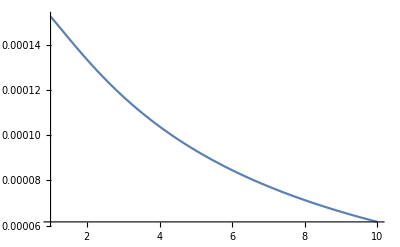

```mathematica
Plot[f[r0],{r0,1,10}]
```

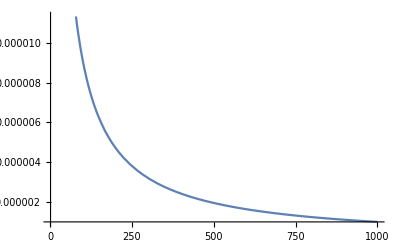

```mathematica
Plot[f[r0],{r0,1,1000}]
```

Evaluating Solution to Integral Numerically

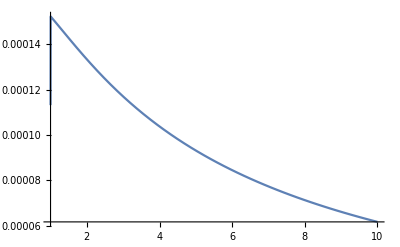

```mathematica
Plot[(I1sol[k]/.{k-> t1/β1,a-> r0/(2π)}),{r0,1,10}]
```

```mathematica
Plot[(I1sol[k]/.{k-> t1/β1,a-> r0/(2π)}),{r0,1,1000}]
```

-Graphics-

The integral I_2 can be solved analytically,

```mathematica
(*Equation 4.116*)
```

```mathematica
Integrate[4*1/x*Sin[(k x)/2]^2*ⅇ^(-n  x),{x,0,∞},Assumptions->{n ϵ Integers, n ≥ 1, k ϵ Reals,k ≥0}]
```

Log[1+k^2/n^2]

```mathematica
I2sol[k_]=Log[Product[1+k^2/n^2,{n,1,∞}]]
```

Log[Sinh[k π]/(k π)]

Asymptotic Early Time Dynamics

In the early time limit t << .1cβ (equivalently k<<.1c1<<.1ca),  the 
integrals I_1 and I_2 can be simplified. Defining a temporary variable f:= 1/a, and series expanding the solution to I_1 (Eq.(4.115)) around f= 0 yields

```mathematica
(*Equation 4.117*)
```

```mathematica
$Assumptions={k>0,k ϵ Reals, r0>1, r0 ϵ Reals};
```

```mathematica
Series[Simplify[I1sol[k]/.a->1/f],{f,0,1}]//Simplify
```

Floor[Arg[f]/(2 π)] (-(ⅈ π)/2-1/2 ⅈ k π f+O[f]^2)+Floor[(π+Arg[f])/(2 π)] (-(ⅈ π)/2+1/2 ⅈ k π f+O[f]^2)+Floor[-Arg[f]/(2 π)] ((ⅈ π)/2+1/2 ⅈ k π f+O[f]^2)+((-k π-Log[1-ⅇ^(-2 k π)]+Log[f]+Log[(2 Sinh[k π])/f])+1/2 k^2 π f+O[f]^2)

```mathematica
Simplify[((-k π-Log[1-ⅇ^(-2 k π)]+Log[f]+Log[(2 Sinh[k π])/f])+1/2 k^2 π f+O[f]^2)/.{ f-> 1/a}]
```

SeriesData::sdatv: First argument 1/a is not a valid variable.

(-k π+Log[1/a]-Log[1-ⅇ^(-2 k π)]+Log[2 a Sinh[k π]])+(k^2 π)/(2 a)+O[1/a]^2

For the I_2 integral, notice there is no a-dependence – hence a series expansion in 1/a yields I_2=O(a)^2. Therefore, in the early time limit, s^2(t) is given by Eq.(4.118). Since s^2(t)∼t^2, the early time dynamics exhibit ballistic behaviour.

Asymptotic Late Time Dynamics

At asymptotically late times,t>>.1dβ (equivalently k>>.1da>>.1d1),
the integrals I_1 and I_2 have the same behaviour. Expanding the solution to I_2 (Eq.(4.116)),  yields

```mathematica
(*Equation 4.120*)
```

```mathematica
Log[TrigToExp[Sinh[k π]]]-Log[k π]
```

Log[-1/2 ⅇ^(-k π)+ⅇ^(k π)/2]-Log[k π]

Therefore, in the late time limit, s^2(t) is given by Eq.(4.121). Since s^2(t)∼t, the late time dynamics exhibit diffusive behaviour. Concretely, at late times s^2(t)  =  2Dt, where D is the diffusion coefficient (Eq.(3.21)).Comparing this to Eq.(4.121), the diffusion coefficient in AdS_3-Schwarzschild is extricated

```mathematica
(*Equation 4.122*)
```

```mathematica
DHQAdS3  =β/(2π √λ);
```

## Analysing Light Quark Brownian Motion (Section 5)

In section (5) an off-mass-shell light quark exhibiting Brownian motion in the thermal plasma is modelled as an open string undergoing transverse fluctuations (initially stretched between the AdS boundary and just above the horizon) whose AdS boundary endpoint is released to fall at the local speed of light in the presence of a space filling D7-brane.  Initially this section focuses on calculating an external light quark’s diffusion coefficient in the bulk AdS_3-Schwarzschild spacetime. Then, importantly, the results are generalised to AdSd-Schwarzschild by expanding and truncating the near-horizon metric.

### Leading Order String Behaviour: Test Strings in R^(1,1) (Subsection 5.1.2)

Consider the Limp Noodle in R^(1,1). The aim of this subsection is to find the embedding functions (X^μ)_Mink(t,σ).

Figure (5)

```mathematica
(*Equation 5.30*)
```

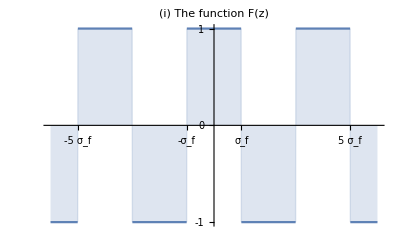

```mathematica
Assumptions  u∈Reals;
F[u_,σ_]:=(-1)^Floor[(u+σ)/(2 σ)] ;
(*Take x-axis to be in units of Subscript[σ, f] i.e. {u,-4 Subscript[σ, f],4 Subscript[σ, f]} *)
G[u_,sig_]:=Plot[F[u,sig],{u,-6 sig,6sig},Filling->Axis,PlotLabel->"(i) The function F(z)",Ticks->{{{-6,} ,{-5,-5 Subscript[σ, f]},{-4,}, {-3,-3 Subscript[σ, f]},{-2,},{-1,-Subscript[σ, f]}, {0,0}, {1,Subscript[σ, f]},{2,},{3,3 Subscript[σ, f]}, {4,},{5,5 Subscript[σ, f]},{6,}},{-1,0,1}} ]
G[u,1]
```

```mathematica
(*Equation 5.31*)
```

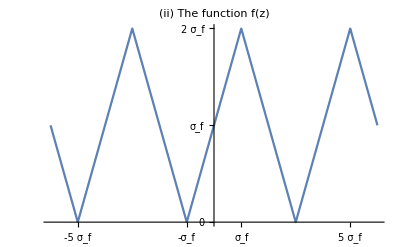

```mathematica
f[u_,σ_]:=NIntegrate[(-1)^Floor[(ui+σ)/(2 σ)],{ui,-σ,u}]
Plot[f[u,1],{u,-6,6},PlotLabel->"(ii) The function f(z)",Ticks->{{{-6,} ,{-5,-5 Subscript[σ, f]},{-4,}, {-3,-3 Subscript[σ, f]},{-2,},{-1,-Subscript[σ, f]}, {0,0}, {1,Subscript[σ, f]},{2,},{3,3 Subscript[σ, f]}, {4,},{5,5 Subscript[σ, f]},{6,}},{0,{1,Subscript[σ, f]},{2,2 Subscript[σ, f]}}} ]
```

### Fluctuating Test String Dynamics: The Limiting Cases of s^2(t) (Subsection 5.2.2.)

The string falling endpoint’s mean-squared transverse displacement can be calculated as

```mathematica
(*Integrand of Equation 5.47*)
```

```mathematica
s2LQ[t_]:=β^2/(4 π^2 √λ)*1/(ⅇ^(β ω)-1)1/ω*(fωLQ[σf-t]-fωLQ[σf] ⅇ^(ⅈ ω t))*Conjugate[fωLQ[σf-t]-fωLQ[σf] ⅇ^(ⅈ ω t)]
```

In the current subsection the string falling endpoint’s mean-squared transverse displacement, s^2(t), is examined in a number of different limiting cases. Videlicet, the small virtuality case and the arbitrary virtuality case. In both of these cases, the asymptotically early time and the asymptotically late time limit is explored. For the arbitrary virtuality case, a further limit of small or large virtuality can be considered.

Small Virtuality (Subsection 5.2.2.1)

In this subsection the behaviour of s^2(t), Eq.(5.47), in the small virtuality limit is considered; and after obtaining a suitable expression for s_small^2(t), the asymptotic early and late time dynamics are explored.
In the small virtuality limit the in-falling (+) and out-going (−) modes of the general solution f_ω(σ) are given by Eq.(5.52). The coefficient B_ω is fixed in the same way as in subsection (4.3.2): by imposing a Neumann boundary condition at the falling string endpoint in the radial direction at t= 0.

```mathematica
(*Equation 5.54*)
```

```mathematica
BωSVsol=Simplify[Expand[Solve[D[Exp[ⅈ*ω*(rsstar+σ)]+BωSV1*Exp[-ⅈ*ω*(rsstar+σ)],σ]==0,BωSV1]]];
BωSVsolEq=BωSV1/.BωSVsol;
BωSV=BωSVsolEq[[1]]/. σ-> σf
```

ⅇ^(2 ⅈ (rsstar+σf) ω)

Hence, the general solution f_ω(σ) is given by,

```mathematica
(*Equation 5.55*)
```

```mathematica
fωSV[σ_]=Exp[ⅈ*ω*(rsstar+σ)]+BωSV*Exp[-ⅈ*ω*(rsstar+σ)]
```

ⅇ^(ⅈ (rsstar+σ) ω)+ⅇ^(-ⅈ (rsstar+σ) ω+2 ⅈ (rsstar+σf) ω)

In order to calculate the falling string endpoint's mean-squared transverse displacement in the small virtuality limit, Eq.(5.55) is substituted into Eq.(5.47)

```mathematica
(*Equation 5.56*)
```

```mathematica
$Assumptions  ={λ∈Reals,λ≥0};
```

```mathematica
s2LQ[t]/. {fωLQ-> fωSV}//ComplexExpand//Simplify
```

(β^2 Sin[t ω]^2)/((-1+ⅇ^(β ω)) π^2 √λ ω)

The integral in Eq.(5.56) can be solved analytically.

```mathematica
(*Equation 5.58*)
```

```mathematica
β^2/(π^2 √λ)Integrate[1/x*Sin[k x]^2*ⅇ^(-n  x),{x,0,∞},Assumptions->{n ϵ Integers, n ≥ 1, k ϵ Reals,k ≥0}] (*where x=βω, and k=t/β*)
```

(β^2 Log[1+(4 k^2)/n^2])/(4 π^2 √λ)

```mathematica
s2LQSV[t_]=β^2/(4 π^2 √λ)Log[Product[1+(4 k^2)/n^2,{n,1,∞}]]/.k-> t/β//Simplify
```

(β^2 Log[(β Sinh[(2 π t)/β])/(2 π t)])/(4 π^2 √λ)

Asymptotic Early Time Dynamics

In the early time limit t << .1cβ,
Eq.(5.58) can be expanded in powers of k=t/β. For small k a Taylor expansion (about k= 0) can be performed

```mathematica
(*Equation 5.59*)
```

```mathematica
s2LQSVEarly[t_]=Series[s2LQSV[k β],{k,0,10}]/.k-> t/β//Simplify
```

SeriesData::sdatv: First argument t/β is not a valid variable.

(β^2 (t/β)^2)/(6 √λ)-((π^2 β^2) (t/β)^4)/(45 √λ)+(16 π^4 β^2 (t/β)^6)/(2835 √λ)-(8 (π^6 β^2) (t/β)^8)/(4725 √λ)+(256 π^8 β^2 (t/β)^10)/(467775 √λ)+O[t/β]^11

Since s^2(t)∼t^2, the early time dynamics exhibit ballistic behaviour.

Asymptotic Late Time Dynamics

In the early time limit t >> .1cβ,
Eq.(5.58) can be expanded in powers of 1/k=β/t.

```mathematica
β^2/(4 π^2 √λ)(Log[TrigToExp[Sinh[2 k π]]]-Log[2k π])
```

(β^2 (Log[-1/2 ⅇ^(-2 k π)+1/2 ⅇ^(2 k π)]-Log[2 k π]))/(4 π^2 √λ)

Therefore, in the late time limit, s^2(t) is given by Eq.(5.60). Since s^2(t)∼t, the late time dynamics exhibit diffusive behaviour. Concretely, at late times s^2(t)  =  2Dt, where D is the diffusion coefficient (Eq.(3.21)). Comparing this to Eq.(5.60), it is easy to see that the diffusion coefficient is given by

```mathematica
(*Equation 5.61*)
```

```mathematica
DLQAdS3  =β/(4π √λ);
```

Arbitrary Virtuality (Subsection 5.2.2.2)

Asymptotic Early Time Dynamics

Now consider a probe light quark with arbitrary virtuality. The behaviour of s^2(t), Eq.(5.47), at asymptotically early times is considered. In the early time limit t << .1cβ,
Eq.(5.47) can be expanded in powers of k=t/β.

```mathematica
(*Integrand of Equation 5.64*)
```

```mathematica
$Assumptions  ={λ∈Reals,λ≥0};
```

```mathematica
s2LQAVEarly=s2LQ[t]/. {fωLQ[σf-t]->fw1[σf,rH,rsstar,r,ω,r/rH,ν,σf] ,fωLQ[σf]-> fw1[σf,rH,rsstar,r,ω,r/rH,ν,σf] }//ComplexExpand//Simplify
```

(4 rH^2 β^2 (1+ν^2) Sin[(t ω)/2]^2)/((-1+ⅇ^(β ω)) π^2 √λ (rH^2+r^2 ν^2) ω)

```mathematica
earlytimesExpand=Series[Sin[(t ω)/2]^2,{t,0,2}]//Normal;
```

```mathematica
s2LQAVEarly/.{Sin[(t ω)/2]^2-> earlytimesExpand}//Simplify
```

(rH^2 t^2 β^2 (1+ν^2) ω)/((-1+ⅇ^(β ω)) π^2 √λ (rH^2+r^2 ν^2))

Eq.(5.64) is evaluated by breaking the integral into two parts and recognising that these terms are the series expansion to (O(k))^0 (around k= 0, where k=t/β) of the second derivatives with respect to k of the integrals I_1 and I_2 given in Eq.(4.112) and Eq.(4.113) respectively.

```mathematica
(*Equation 5.65*)
```

```mathematica
DI12=Series[D[I1,{k,2}],{k,0,0}]/.{ x-> 2 π ν, a-> r0/(2 π)}//Normal
```

(4 π ν)/((-1+ⅇ^(2 π ν)) (1+r0^2 ν^2))

```mathematica
(*Equation 5.66*)
```

```mathematica
DI22=Series[D[I2,{k,2}],{k,0,0}]/.{ x-> 2 π ν, a-> r0/(2 π)}//Normal
```

(4 π ν)/(-1+ⅇ^(2 π ν))

```mathematica
(*Equation 5.67*)
```

```mathematica
s2LQAVEarly2=t^2/(π√λ)Simplify[(((r0^2-1)/r0^2)*DI12+(1/r0^2)*DI22)]
```

(4 t^2 ν (1+ν^2))/((-1+ⅇ^(2 π ν)) √λ (1+r0^2 ν^2))

The solution to the integrals I_1 and I_2 are given by Eqs.(4.115, 4.116) respectively.  Taking the second derivative with respect to k followed by a series expansion to (O(k))^0 (around k=  0) for each of these solutions, yields

```mathematica
$Assumptions={k>0,k ϵ Reals, r0>1, r0 ϵ Reals};
```

```mathematica
(*Equation 5.68*)
```

```mathematica
(*Since we are working with the physically relevant case t≥0, we know that β>0 (early times case t<<β). Therefore k=t/β≥0. Hence, Abs[k]=k.*)
I1i[k_]=Simplify[I1sol[k]/. Abs[k]->k];
I1i''[k];(*Second derivative*)
I1d2k0=Series[I1i''[k],{k,0,0}]//Normal
```

(2 π Cot[1/(2 a)]+Log[-1/a]+Log[1/a]-Log[-a]-Log[a]-4 Log[2 π]-2 PolyGamma[0,1-1/(2 a π)]-2 PolyGamma[0,1+1/(2 a π)])/(4 a^2)

```mathematica
(*Equation 5.69*)
```

```mathematica
I2sol''[k];(*Second derivative*)
I2d2k0=Series[I2sol''[k],{k,0,0}]//Normal(*Second derivative evaluated at k =0*)
```

π^2/3

Inputting Eq.(5.68) and Eq.(5.69) into Eq.(5.67), yields the transverse mean-squared displacement in the early time limit

```mathematica
(*Equation 5.70*)
```

```mathematica
s2LQAVEarly3[t_,r0_,λ_]=1/2 t^2/(π^2 √λ)*Simplify[((4 π^2 a^2-1)/(4 π^2 a^2)*I1d2k0+1/(4 π^2 a^2)*I2d2k0)/.{ a-> r0/(2 π)}]
```

(t^2 (r0^2+6 (-1+r0^2) (π Cot[π/r0]-2 Log[r0]-PolyGamma[0,1+1/r0]-PolyGamma[0,(-1+r0)/r0])))/(6 r0^4 √λ)

```mathematica
(*Recognizing that the digamma functions are related to the harmonic numbers: Ψ(n) = Subscript[H, (n-1)]- Subscript[γ, E] (where Subscript[γ, E]  is the Euler-Masheroni constant and n is a positive interger)*)
s2LQAVEarly4[t_,r0_,λ_]=s2LQAVEarly3[t,r0,λ]/. {PolyGamma[0,1+1/r0] -> (HarmonicNumber[1/r0] - EulerGamma), PolyGamma[0,(-1+r0)/r0] -> (HarmonicNumber[-1/r0] - EulerGamma)}//Simplify;
(*which agrees with Eq.(3.42) in Moerman et al. [2]*)
```

The integral s2LQAVEarly2 can be numerically evaluated (to prove the solution is indeed given by s2LQAVEarly3.

Evaluating Integral Numerically

```mathematica
λ1 = 10 ;
```

```mathematica
f[r0_]:=(4 t1^2)/(√λ1)*NIntegrate[(ν (1+ν^2))/((-1+ⅇ^(2 π ν)) (1+r0^2 ν^2)),{ν,0,∞}]
```

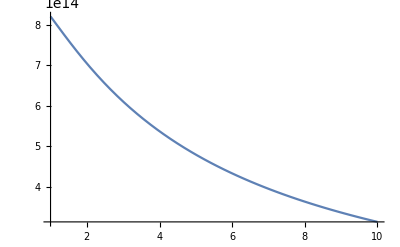

```mathematica
Plot[f[r0],{r0,1,10}]
```

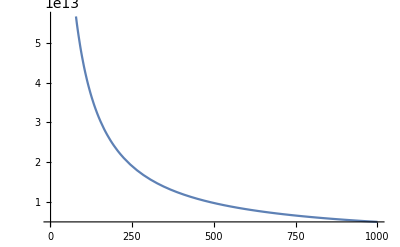

```mathematica
Plot[f[r0],{r0,1,1000}]
```

Evaluating Solution to Integral Numerically

```mathematica
Plot[s2LQAVEarly3[t1,r0,λ1],{r0,1,10}]
```

-Graphics-

```mathematica
Plot[s2LQAVEarly3[t1,r0,λ1],{r0,1,1000}]
```

-Graphics-

Small Virtuality

Take the limit of Eq.(5.70) as (r̃)_0→1 + ϵ̃

```mathematica
(*Equation 5.71*)
```

```mathematica
Limit[s2LQAVEarly3[t,r0,λ],r0->1]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

t^2/(6 √λ)

This agrees exactly with Eq.(5.59), i.e. taking the early time limit followed by the small virtuality limit is equivalent to taking small virtuality limit followed by the early time limit – a necessary consistency check.

Large Virtuality

Since (r̃)_0>>0, define a variable y=  1/(r̃)_0 (where y<<.1c0) so that a Taylor expansion 
in y can be performed. Rewriting Eq.(5.70) in terms of y and performing a series expansion (around y= 0), yields

```mathematica
(*Equation 5.72*)
```

```mathematica
(* Define variable x=1/r0, when r0 -> ∞, x<<0 and we can perform a taylor expansion in x*)
Simplify[Series[s2LQAVEarly3[t,1/x,λ],{x,0,3}] /.x->1/r0]
```

SeriesData::sdatv: First argument 1/r0 is not a valid variable.

t^2/(√λ r0)+(t^2 (1+12 EulerGamma-12 Log[r0]) (1/r0)^2)/(6 √λ)-(((3+π^2) t^2) (1/r0)^3)/(3 √λ)+O[1/r0]^4

As expected, the large virtuality early time behaviour corresponds exactly with the early time limit of the on-mass-shell heavy quark (i.e. the static string solution at early times, Eq.(4.121))

Late Time Dynamics

The behaviour of s^2(t), Eq.(5.47), at asymptotically late times is considered. Defining two dimensionless quantities u:= β/t=1/k, and z:= ω t, the late time dynamics of s^2(t) can be examined

```mathematica
(*Equation 5.75*)
```

```mathematica
Simplify[ComplexExpand[fw1[(σf-β/x),rH,rsstar,rH,z/t,1,ν,σf]*fwconj1[(σf-β/x),rH,rsstar,rH,z/t,1,ν,σf]-fw1[(σf-β/x),rH,rsstar,rH,z/t,1,ν,σf]*fwconj1[σf,rH,rsstar,rH,z/t,1,ν,σf]*Exp[-ⅈ z] - fw1[σf,rH,rsstar,rH,z/t,1,ν,σf]*fwconj1[(σf-β/x),rH,rsstar,rH,z/t,1,ν,σf]*Exp[ⅈ z]+ fw1[σf,rH,rsstar,rH,z/t,1,ν,σf]*fwconj1[σf,rH,rsstar,rH,z/t,1,ν,σf]]/. {z-> ω t,β-> t x}] (*Near horizon limit r=rH, therefore r0=1*)
```

4 Sin[t ω]^2

Substituting Eq.(5.75) into Eq.(5.74), yields (s^2(t))_(t>>β) = (s^2)_small(t) (Eq.(5.76)). Therefore, the late time dynamics of an arbitrary virtuality light quark in a thermal plasma is diffusive (s^2)_small(t)∼t, and the diffusion coefficient is given by Eq.(5.61). This statement can be made due to a key insight of Moerman et al.[2] – that the integral in Eq.(5.76) is identical to (s^2)_small(t), the string falling endpoint’s mean-squared transverse displacement in the limit of small virtualities (see subsection (5.2.2.1)). This allows them to conclude that the behaviour of arbitrary virtuality quarks at asymptotically late times (i.e. in the near-horizon region) is encoded in the small virtuality case. This is intuitive, since the length of the Limp Noodle is arbitrarily short at asymptotically late times. Since (s^2)_small(t;d) can be solved for any dimensions d≥3 in AdS_d-Schwarzschild, the late time behaviour (and therefore the diffusion coefficient) of Limp Noodles with arbitrary length (equivalently, light quarks of arbitrary virtuality) in any number of transverse spatial dimensions are able to be determined. This generalisation to AdS_d-Schwarzschild is presented in subsection (5.3). See Mathematica Notebook ‘NearHorizonAdSd.nb’ for details pertaining to this calculation.

### Interpolating between the on-mass-shell and off-mass-shell results for s^2(t)

Moerman et al.postulated in [2] that by introducing a factor a which determines the fraction of the local speed of light the boundary endpoint of the test string falls at, a general expression can be found for the mean-squared displacement of said endpoint (and therefore the diffusion coefficient) which interpolates between the heavy and light quark results. Explicitly, the string falling endpoint's mean-squared transverse displacement is given by

```mathematica
s2LQaIntegrand[β_,z_,d_]:=(d-1)^2/4 β^2/(4 π^2 √λ)*1/(ⅇ^(z x)-1)1/ω*(fωLQ[σf-a β/x]-fωLQ[σf] ⅇ^(ⅈ z))*Conjugate[fωLQ[σf-a β/x]-fωLQ[σf] ⅇ^(ⅈ z)]
```

```mathematica
$Assumptions  ={λ∈Reals,λ≥0};
s2LQaIntegrand2=ComplexExpand[s2LQaIntegrand[β,z,d]/. {fωLQ[σf-a β/x]->fw1[(σf-a β/x),rH,rsstar,rH,z/t,1,ν,σf] ,fωLQ[σf]-> fw1[σf,rH,rsstar,rH,z/t,1,ν,σf]}]/.{z-> ω t,β-> t x }//Simplify
```

((-1+d)^2 t^2 x^2 (3-2 Cos[(-1+a) t ω]+Cos[2 a t ω]-2 Cos[(1+a) t ω]))/(8 (-1+ⅇ^(t x ω)) π^2 √λ ω)

```mathematica
ssmall2Integrand[a_,k_,t_,λ_,d_]:=(d-1)^2/4 t^2/(π^2 √λ k^2)*1/(ⅇ^(β ω)-1)(1+Cos[a ω t]^2-2Cos[a ω t]Cos[ω t]) (*which is equal to s2LQaIntegrand2 -> use the sum/difference cosine trigonometric identities to see the equivalence.*)
```

Manipulating the above equation (in a similar way to Eq.(5.58)) and integrating, yields

```mathematica
ssmall2int[a_,k_,t_,λ_,d_]=(d-1)^2/4 t^2/(π^2 √λ k^2)*Integrate[1/x*(2-Sin[a k x]^2-(Cos[(a-1) k x]+Cos[(a+1)k x]))*ⅇ^(-n  x),{x,0,∞},Assumptions->{n ϵ Integers, n ≥ 1, k ϵ Reals,k ≥0, a ϵ Reals,a≥0, a≤1}] (*Change of variables made using x=βω, and k=t/β*)
```

((-1+d)^2 t^2 (-6 Log[n]-Log[4 a^2 k^2+n^2]+2 Log[((-1+a)^2 k^2+n^2) ((1+a)^2 k^2+n^2)]))/(16 k^2 π^2 √λ)

```mathematica
ssmall2int2[a_,k_,d_]=(d-1)^2/4 t^2/(π^2 √λ k^2)*1/4 Log[Product[n^-6*(4 a^2 k^2+n^2)^-1*(((-1+a)^2 k^2+n^2) ((1+a)^2 k^2+n^2))^2,{n,1,∞}]]/.{x-> β ω,k-> t/β}//Simplify
```

((-1+d)^2 β^2 Log[(a β^3 (Cosh[(2 π t)/β]-Cosh[(2 a π t)/β])^2 Csch[(2 a π t)/β])/(2 (-1+a^2)^2 π^3 t^3)])/(16 π^2 √λ)

Manipulating ssmall2int2[a,k,d] into a manageable expression yields

```mathematica
(*Equation 6.42*)
```

```mathematica
ssmall2[a_,t_,λ_,β_,d_]:=(d-1)^2/4 β^2/(4 π^2 √λ)*Log[(2a β^3 Sinh[(π (a+1)t)/β]^2 Sinh[(π (a-1)t)/β]^2 Csch[(2 a π t)/β])/((-1+a^2)^2 π^3 t^3)];
```

which, at late times, becomes

```mathematica
(*Equation 6.43*)
```

Case 1: a=1

```mathematica
ssmall2intLate[a_,k_,d_]=ssmall2int[1,k,t,λ,d]
```

((-1+d)^2 t^2 (-6 Log[n]-Log[4 k^2+n^2]+2 Log[n^2 (4 k^2+n^2)]))/(16 k^2 π^2 √λ)

```mathematica
ssmall2intLate2[a_,k_,d_]=((d-1)^2 t^2)/(16 k^2 π^2 √λ) Log[Product[n^-6*(4 k^2+n^2)^-1*( n^2(4 k^2+n^2))^2,{n,1,∞}]]/.{x-> β ω , k -> t/β}//Simplify
```

((-1+d)^2 β^2 Log[(β Sinh[(2 π t)/β])/(2 π t)])/(16 π^2 √λ)

```mathematica
(*Agrees with Eq.(5.58) for d=3, which we have already proved goes like Subscript[s^2, small] ->βt/(2π√λ)+β^2/(4 π^2 √λ)Log[β/(4πt)]+O[1], in the late time limit (Eq.(5.60)). i.e. Subscript[s^2, small] ->(d-1)^2/4(βt/(π√λ)[1-a/2]+β^2/(4 π^2 √λ)Log[β/(4πt)]+O[(β/t)^0]) when a=1.*)
```

Case 2: a=0

```mathematica
ssmall2intLatea0[a_,k_,d_]=ssmall2int[0,k,t,λ,d]
```

((-1+d)^2 t^2 (-6 Log[n]-Log[n^2]+2 Log[(k^2+n^2)^2]))/(16 k^2 π^2 √λ)

```mathematica
ssmall2intLatea02[a_,k_,d_]=((d-1)^2 t^2)/(16 k^2 π^2 √λ)Log[Product[n^-6*(n^2)^-1*(k^2+n^2)^4,{n,1,∞}]]/.{x-> β ω , k -> t/β}//Simplify
```

((-1+d)^2 β^2 Log[(β^4 Sinh[(π t)/β]^4)/(π^4 t^4)])/(16 π^2 √λ)

```mathematica
(* Hence, Subscript[s^2, small] = ((-1+d)^2 β^2)/(4 π^2 √λ)Log[(β Sinh[(π t)/β])/(π t)]. Perfoming a similar calculation as in Eq.(5.60), in the late time limit Subscript[s^2, small] ->(d-1)^2/4(βt/(π√λ)+β^2/(π^2 √λ)Log[β/(2πt)]+O[1]),i.e. Subscript[s^2, small] ->(d-1)^2/4(βt/(π√λ)[1-a/2]+β^2/(4 π^2 √λ)(4Log[β/(2πt)])+O[(β/t)^0]) when a=0.*)
```

Case 3: 0 < a < 1

```mathematica
ssmall2Late0a1[a_,k_,d_]=TrigToExp[ssmall2[a,t,λ,β,d]]
```

((-1+d)^2 β^2 Log[(a (-ⅇ^(-((-1+a) π t)/β)+ⅇ^(((-1+a) π t)/β))^2 (-ⅇ^(-((1+a) π t)/β)+ⅇ^(((1+a) π t)/β))^2 β^3)/(4 (-1+a^2)^2 (-ⅇ^(-(2 a π t)/β)+ⅇ^((2 a π t)/β)) π^3 t^3)])/(16 π^2 √λ)

```mathematica
(*We can neglect the -ⅇ^(-(π t)/β) terms, since t/β -> ∞. 
Therefore: Subscript[s^2, small] -> β^2/(4 π^2 √λ) (Log[((-ⅇ^(-((-1+a) π t)/β)+ⅇ^(((-1+a) π t)/β))^2 (-ⅇ^(-((1+a) π t)/β)+ⅇ^(((1+a) π t)/β))^2)/(-ⅇ^(-(2 a π t)/β)+ⅇ^((2 a π t)/β))]+Log[aβ^3/(4 π^3(-1+a^2)^2 t^3)])
					= β^2/(4 π^2 √λ) (2*Log[-ⅇ^(-((-1+a) π t)/β)+ⅇ^(((-1+a) π t)/β)] + 2*Log[-ⅇ^(-((1+a) π t)/β)+ⅇ^(((1+a) π t)/β)] -Log[-ⅇ^(-(2 a π t)/β)+ⅇ^((2 a π t)/β)] + Log[aβ^3/(4 π^3(-1+a^2)^2 t^3)]) 
				  -> β^2/(4 π^2 √λ) (2*Log[-ⅇ^(-((-1+a) π t)/β)] + 2*Log[ⅇ^(((1+a) π t)/β)] -Log[ⅇ^((2 a π t)/β)] + Log[aβ^3/(4 π^3(-1+a^2)^2 t^3)]). 
Simplifying this expression yields: Subscript[s^2, small] -> β^2/(4 π^2 √λ) ((4πt)/β[1-a/2]+Log[aβ^3/(4 π^3(-1+a^2)^2 t^3)]) = βt/(π √λ)[1-a/2]+β^2/(4 π^2 √λ)Log[aβ^3/(4 π^3(-1+a^2)^2 t^3)]. This agrees with Eq.115 (0<a<1), where the coeffcient of the first term is [1-a/2].*)
```

The diffusion coefficient for a quark in a (d−1)-dimensional thermal plasma can be extracted from Eq.(6.43). Specifically,

```mathematica
(*Equation 6.44*)
```

```mathematica
DiffCoeff[a_,d_]:=(1-a/2)*((d-1)^2 β)/(8 π √λ)
```

### References

[1] J. de Boer, V. Hubeny, M. Rangamani, and M. Shigemori.  Brownian Motion in AdS/CFT.Journal of High Energy Physics, 2009(07):094–094, (2009).  doi:10.1088/1126-6708/2009/07/094. arXiv:0812.5112 [hep-th].
[2] R. Moerman and W. Horowitz. A Semi-classical Recipe for Wobbly Limp Noodles in Partonic Soup.arXiv preprint, (2016).arXiv:1605.09285 [hep-th].